```mathematica
(*Generalized b distribution*)

Remove["Global`*"]

eq1= {vMean'[t] == -vMean[t]/tauv + f*bMean[f], vMean[0] == 0};
sol= FullSimplify[DSolve[eq1, vMean[t], t]] ;
vMean[t_] = vMean[t] /. First[sol];
eq2 ={vSquaredMean'[t] == (-2/tauv)*vSquaredMean[t] + 2*f*bMean[f]*vMean[t]+ f*bSquaredMean[f], vSquaredMean[0] == 0};
sol = FullSimplify[DSolve[eq2, vSquaredMean[t], t]];
Print["vSquaredMean"];
vSquaredMean[t_] = vSquaredMean[t] /. First[sol];



vMean0 = 0;
vSquaredMeanTMean[f_] = vSquaredMean[Tmean[f]];
vTmean = vth;
CVvSquaredTmean[f_] =  (vSquaredMeanTMean[f] - vTmean^2)/vTmean^2;
(*dvdtMean= -vth/tauv;*)
dvdtMean[f_] = -1/tauv*vth + f bMean[f];
Print["<T>"]
Tmean [f_]= tauv*Log[(1-vMean0/(tauv*f*bMean[f]))/(1-vth/(tauv*f*bMean[f]))]
Print["CVT2"]
CVTsquared[f_] = FullSimplify[vth^2/(Tmean[f]^2)*dvdtMean[f]^(-2)*CVvSquaredTmean[f]]
```

vSquaredMean

<T>

tauv Log[1/(1-vth/(f tauv bMean[f]))]

CVT2

-(vth (vth-2 f tauv bMean[f]) bSquaredMean[f])/(2 f tauv bMean[f]^2 (vth-f tauv bMean[f])^2 Log[1+vth/(-vth+f tauv bMean[f])]^2)

```mathematica
tauv Log[1/(1-((k+f pr) vth)/(c f k M pr tauv))]
```

CVT2

-((k+f pr) (-1+k (-1+pr)+f (-1+pr) pr) vth (2 c f k M pr tauv-(k+f pr) vth))/(2 f k M pr tauv (c f k M pr tauv-(k+f pr) vth)^2 Log[(c f k M pr tauv)/(c f k M pr tauv-(k+f pr) vth)]^2)

CVT2

<T>

CVT2

<T>

1907.68

0.13

3

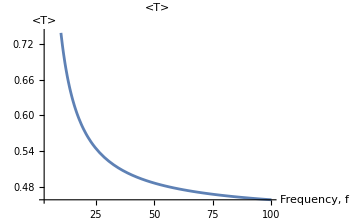
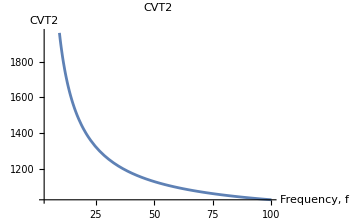

```mathematica
tauv = 1;
c = 0.02;
vth = 0.07;
pr = 0.2;
M = 10;
k = 1;

CVTsquared[10]

checkvth =c k M tauv - vth
checkf = vth k / (pr*(c k M tauv - vth));
ninit = Ceiling[checkf]

fmax = 100;
p1 = Plot[Tmean[f],{f,ninit,fmax},PlotLabel->("<T>"), AxesLabel  -> {"Frequency, f", "<T>"}, ImageSize -> Medium];
p2 = Plot[CVTsquared[f], {f, ninit, fmax},PlotLabel->("CVT2"), AxesLabel-> {"Frequency, f", "CVT2"}, ImageSize -> Medium];
Row[{p1, p2}]
```

```mathematica
0
```

0

```mathematica
(*Generalized b distribution*)

Remove["Global`*"]

(*General moments*)
bMean[f_] = c pr k M /(f pr + k);
bSquaredMean[f_] = c^2*(pr*(1-pr)*k M / (f pr + k) + (pr*k*M/(f pr + k)^2));

eq1= {vMean'[t] == -vMean[t]/tauv + f*bMean[f], vMean[0] == 0};
sol= FullSimplify[DSolve[eq1, vMean[t], t]] ;
vMean[t_] = vMean[t] /. First[sol];

vMean0 = 0;
TmeanOL [f_]= tauv*Log[(1-vMean0/(tauv*f*bMean[f]))/(1-vth/(tauv*f*bMean[f]))]

p[f_] = 1/(f*TmeanOL[f])
```

tauv Log[1/(1-((k+f pr) vth)/(c f k M pr tauv))]

1/(f tauv Log[1/(1-((k+f pr) vth)/(c f k M pr tauv))])

```mathematica
(*
k and M and c as a function of f
*)

Remove["Global`*"]

(*eq1 = {nMean'[t] == k M - (k + f Subscript[p, r])*nMean[t], nMean[0] == 0};*)
eq2 = {nSquaredMean'[t] == k*M +(2 k M - k + f Subscript[p, r]*(1 - Subscript[p, r]))* nMean + (f Subscript[p, r]^2 - 2 f Subscript[p, r] - 2k)nSquaredMean[t], nSquaredMean[0] == 0};
eq3 = {vMean'[t] == -vMean[t]/Subscript[tau, v] + f*Subscript[c, u]*Subscript[p, r]*nMean, vMean[0] == 0};
eq4 = {nvMean'[t] == k*M*vMean[t] - Subscript[c, u]*f*Subscript[p, r]*(1-Subscript[p, r])*nMean + Subscript[c, u]^2*f*Subscript[p, r]^2*nSquared[t] + 2*f*Subscript[c, u]*Subscript[p, r]*nvMean[t], nvMean[0] == 0};
eq5 = {vSquaredMean'[t] == -t/Subscript[tau, v] vSquaredMean[t] + Subscript[c, u]^2*f*Subscript[p, r]*(1-Subscript[p, r])*nMean+ Subscript[c, u]^2*f*Subscript[p, r]^2*nSquaredMean[t] + 2*f*Subscript[c, u]*Subscript[p, r]*nvMean[t], vSquaredMean[0] == 0};
```

```mathematica
(*sol1 = DSolve[eq1, nMean[t], t];
nMean[t_] = nMean[t] /. First[sol1];*)

nMean = k*m/(f*Subscript[p, r]+k);
sol2 = DSolve[eq2, nSquaredMean[t], t];
nSquaredMean[t_] = nSquaredMean[t] /. First[sol2];
sol3 = DSolve[eq3, vMean[t], t];
vMean[t_] = vMean[t] /. First[sol3];
sol4 = DSolve[eq4, nvMean[t], t];
nvMean[t_] = nvMean[t] /. First[sol4];
sol5 = DSolve[eq5, vSquaredMean[t], t];
vSquaredMean[t_] = vSquaredMean[t] /. First[sol5];
```

```mathematica
k = 20;
Subscript[c, u] = 10;
M = 20;
Subscript[p, r]= 0.4;
Subscript[v, th] = 0.2;
Subscript[p, d] = 0.4;

Subscript[dvdt, mean] = Subscript[v, th]/Subscript[tau, v];
Subscript[v, max] [f_] = k Subscript[c, u] f M Subscript[p, r] Subscript[tau, v] / (f Subscript[p, r] + k);
Subscript[T, mean][f_] = Subscript[tau, v]*Log[(1 + Subscript[c, d]*Subscript[M, d]*Subscript[p, d] / (Subscript[v, max]))/(1 - Subscript[v, th]/Subscript[v, max])]
Subscript[CV2, v][f_] = (vSquaredTmean - Subscript[v, th]^2)/(Subscript[v, th]^2)
Subscript[CV2, T][f_] = Subscript[v, th]/Subscript[T, mean][f]^2*(Subscript[dvdt, mean])^{-2}*Subscript[CV2, v][f]
```

Log[(1+(0.4 20_d c_d)/v_max)/(1-0.2/v_max)] tau_v

25. (-0.04+vSquaredTmean)

{(125. (-0.04+vSquaredTmean))/Log[(1+(0.4 20_d c_d)/v_max)/(1-0.2/v_max)]^2}

```mathematica
Plot[TMean[f], {f, 1, 100}]
Plot[Subscript[CV2, T][f], {f, 1, 100}]
```

-Graphics-

-Graphics-

```mathematica
(* 
v'(t) = 0
*)
Remove["Global`*"]

bMeanSS = Subscript[p, r] k M / (f Subscript[p, r] + k);
bVarianceSS = Subscript[p, r] (1-Subscript[p, r]) k M / (f Subscript[p, r] + k);
bSquaredMeanSS = FullSimplify[bVarianceSS+ bMeanSS^2];

eq1 = {vMean'[t] == c*f*bMeanSS, vMean[0] == 0};
sol1 = DSolve[eq1, vMean[t], t];
vMean[t_] = vMean[t] /. First[sol1];

eq2 = {vSquared'[t] == 2*c*f*bMeanSS*vMean[t]+ f*c^2*bMeanSS^2, vSquared[0] == 0};
sol2 = DSolve[eq2, vSquared[t], t] ;
Print["vSquared"]
vSquared[t_] = vSquared[t] /. First[sol2]

CVvSquared[f_] = (vSquared[Tmean[f]] - vth^2)/(vth^2);
dvdtTmean[f_] = c*f*bMeanSS;

Print["Tmean"]
Tmean[f_] = vth/(c*f*bMeanSS)
Print["CVT2"]
CVTSquared[f_] = vth^2/Tmean[f]^2*(dvdtTmean[f])^(-2)*CVvSquared[f]
```

vSquared

(c^2 f k^2 M^2 (t+f t^2) p_r^2)/(k+f p_r)^2

Tmean

(vth (k+f p_r))/(c f k M p_r)

CVT2

(-vth^2+(c^2 f k^2 M^2 p_r^2 ((vth (k+f p_r))/(c f k M p_r)+(vth^2 (k+f p_r)^2)/(c^2 f k^2 M^2 p_r^2)))/(k+f p_r)^2)/vth^2

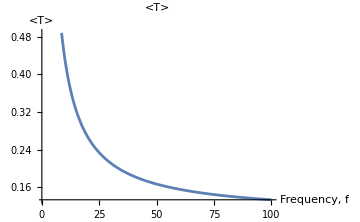
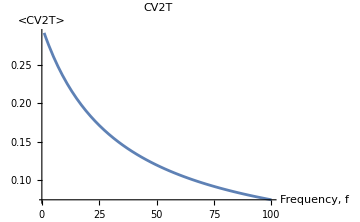

```mathematica
vth = 0.2;
c = 0.02;
bMean = 100;
fmax = 100;
k = 10;
M = 10;
Subscript[p, r] = 0.3;

p1 = Plot[Tmean[f], {f, 1, fmax},PlotLabel->("<T>"),AxesLabel  -> {"Frequency, f", "<T>"}, ImageSize -> Medium];
p2 = Plot[CVTSquared[f], {f, 1, fmax}, PlotLabel->("CV2T"), AxesLabel  -> {"Frequency, f", "<CV2T>"}, ImageSize -> Medium];
Row[{p1, p2}]
```

```mathematica
R = p;
eq = FullSimplify[b12*R-b1^2R^2 + b22*(1-R)^2 + b2^2*(1-R)^2]
```

b2^2 (-1+p)^2+b22 (-1+p)^2+p (b12-b1^2 p)

```mathematica
(* -------------Excitatory and Inhibitatory -------------------------------*)
Remove["Global`*"]

b1MeanSS[f_] = p1*k1*M1/(f*p1+k1);
b2MeanSS[f_] = p2*k2*M2/(f*p2+k2);
bMeanSS[f_] = c1*b1MeanSS[f]*pe-c2*b2MeanSS[f]*(1-pe);

bSquaredMeanSS[f_] = c1^2*pe*(1-p1)*b1MeanSS[f]+c2^2*(1-pe)*(1-p2)*b2MeanSS[f] + (c1*b1MeanSS[f]*pe-c2*b2MeanSS[f]*(1-pe))^2;

eq1= {vMean'[t] == -vMean[t]/tauv + f*bMeanSS[f], vMean[0] == 0};
sol= DSolve[eq1, vMean[t], t] ;
vMean[t_] = vMean[t] /. First[sol];
eq2 ={vSquaredMean'[t] == (-2/tauv)*vSquaredMean[t] + 2*f*bMeanSS[f]*vMean[t]+ f*bSquaredMeanSS[f], vSquaredMean[0] == 0};
sol = FullSimplify[DSolve[eq2, vSquaredMean[t], t]];
vSquaredMean[t_] = vSquaredMean[t] /. First[sol];

vMean0 = 0;
vSquaredMeanTMean[f_] = vSquaredMean[Tmean[f]];
vTmean = vth;
CVvSquaredTmean[f_] =  (vSquaredMeanTMean[f] - vTmean^2)/vTmean^2;
dvdtMean[f_] = -1/tauv*vth + f bMeanSS[f];
Print["<T>"]
Tmean [f_]= tauv*Log[(1-vMean0/(tauv*f*bMeanSS[f]))/(1-vth/(tauv*f*bMeanSS[f]))]
Print["CVT2"]
CVTsquared[f_] = FullSimplify[vth^2/(Tmean[f]^2)*dvdtMean[f]^(-2)*CVvSquaredTmean[f]]
```

<T>

tauv Log[1/(1-vth/(f (-(c2 k2 M2 p2 (1-pe))/(k2+f p2)+(c1 k1 M1 p1 pe)/(k1+f p1)) tauv))]

CVT2

$Aborted

```mathematica
CV2T
```

CV2T

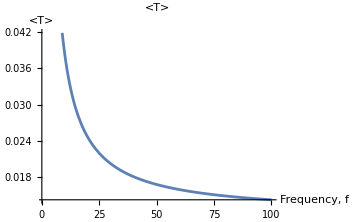
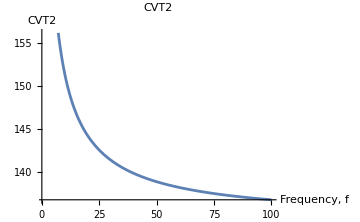

```mathematica
tauv = 1;
vth = 0.2;
p1 = 0.5;
p2 = 0.3;
M1= 100;
M2 = 100;
k1 = 10;
k2 = 1;
pe = 0.9;
c1 = 0.02;
c2 = 0.09;

fmax = 100;
plt1 = Plot[Tmean[f],{f,1,fmax},PlotLabel->("<T>"), AxesLabel  -> {"Frequency, f", "<T>"}, ImageSize -> Medium];
plt2 = Plot[CVTsquared[f], {f, 1, fmax},PlotLabel->("CVT2"), AxesLabel-> {"Frequency, f", "CVT2"}, ImageSize -> Medium];
Row[{plt1, plt2}]
```

```mathematica
FunctionSingularities[Tmean[f], f, Reals]
```

-0.27/(1+0.3 f)+9./(10+0.5 f)==0||-0.2/((-0.27/(1+0.3 f)+9./(10+0.5 f)) f)==-1||0.3 f==-1||0.5 f==-10||f==0||1-0.2/((-0.27/(1+0.3 f)+9./(10+0.5 f)) f)<0

```mathematica
Reduce[vth > f tauv (p1 k1 M1 / (f p1 + k1))*pe - p2 k2 M2 / (f p2 + k2) * (1 - pe), f]
```

```mathematica
(*--------------------Incoherent feed-forward network----------------------*)
Remove["Global`*"]
b1MeanSS[f_] =  p1 k1 M1 / (f p1 + k1);
b2MeanSS[f_] = p2 k2 M2 / (f p2 + k2);
bMeanSS[f_] = c1*p1*k1*M1/(f*p1+k1)-c2*p2*k2*M2/(f*p2*k2)*pi;
bVarianceSS[f_] = c1^2*(1-p1)*b1MeanSS[f]+c2^2*pi*(1-p2)*b2MeanSS[f];
bSquaredMeanSS[f_] = FullSimplify[bVarianceSS[f]+ bMeanSS[f]^2];

eq1= {vMean'[t] == -vMean[t]/tauv + f*bMeanSS[f], vMean[0] == 0};
sol= DSolve[eq1, vMean[t], t];
vMean[t_] = vMean[t] /. First[sol];
eq2 ={vSquaredMean'[t] == (-2/tauv)*vSquaredMean[t] + 2*f*bMeanSS[f]*vMean[t]+ f*bSquaredMeanSS[f], vSquaredMean[0] == 0};
sol = FullSimplify[DSolve[eq2, vSquaredMean[t], t]];
Print["VSquaredMean"]
vSquaredMean[t_] = vSquaredMean[t] /. First[sol];

vMean0 = 0;
vSquaredMeanTMean[f_] = vSquaredMean[Tmean[f]];
vTmean = vth;
CVvSquaredTmean[f_] =  (vSquaredMeanTMean[f] - vTmean^2)/vTmean^2;
dvdtMean[f_] = -1/tauv*vth + f*bMeanSS[f];
Print["<T>"]
Tmean [f_]= tauv*Log[(1-vMean0/(tauv*f*MeanSS[f]))/(1-vth/(tauv*f*bMeanSS[f]))]
Print["CVT2"]
CVTsquared[f_] = FullSimplify[vth^2/(Tmean[f]^2)*dvdtMean[f]^(-2)*CVvSquaredTmean[f]]
```

VSquaredMean

<T>

tauv Log[1/(1-vth/(f ((c1 k1 M1 p1)/(k1+f p1)-(c2 M2 pi)/f) tauv))]

CVT2

((k1+f p1)^2 (-vth^2-(vth (c2^2 M2 (k1+f p1)^2 pi (f^2 k2 (-1+p2) p2-M2 (k2+f p2) pi) (2 c1 f k1 M1 p1 tauv-(k1+f p1) (2 c2 M2 pi tauv+vth))-f (k2+f p2) (2 c1^3 f^2 k1^2 M1^2 p1^2 (k1+k1 (-1+M1) p1-f (-1+p1) p1) tauv+2 c2^2 M2^2 (k1+f p1)^3 pi^2 tauv vth+2 c1 c2 k1 M1 M2 p1 (k1+f p1)^2 pi (2 c2 M2 pi tauv+vth-2 f tauv vth)+c1^2 f k1 M1 p1 (k1+f p1) (-2 c2 M2 (k1+k1 (-1+3 M1) p1-f (-1+p1) p1) pi tauv+(f (-1+p1) p1+k1 (-1+p1+M1 p1 (-1+2 f tauv))) vth))))/(2 f (k1+f p1) (k2+f p2) (c1 f k1 M1 p1-c2 M2 (k1+f p1) pi)^2 tauv)))/((c1 f k1 M1 p1 tauv-(k1+f p1) (c2 M2 pi tauv+vth))^2 Log[1/(1-((k1+f p1) vth)/((c1 f k1 M1 p1-c2 M2 (k1+f p1) pi) tauv))]^2)

Sin[pi]

```mathematica
ToPythonFunction[CVTSquared]
```

ToPythonFunction[CVTSquared]

```mathematica
Solve[x-tauv Log[1/(1-vth/(f tauv*(A-B/x) ))]==0, x]
```

$Aborted

```mathematica
Solve[x^2+a x+1==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[x-tauv Log[1/(1-A/x)]==0,x]

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------- Characterizing the general forms -----------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Remove["Global`*"]
eq1= {vMean'[t] == -vMean[t]/tauv + f*bMean[f], vMean[0] == 0};
sol= FullSimplify[DSolve[eq1, vMean[t], t]] ;
vMean[t_] = vMean[t] /. First[sol];
eq2 ={vSquaredMean'[t] == (-2/tauv)*vSquaredMean[t] + 2*f*bMean[f]*vMean[t]+ f*bSquaredMean[f], vSquaredMean[0] == 0};
sol = FullSimplify[DSolve[eq2, vSquaredMean[t], t]];
Print["vSquaredMean"];
vSquaredMean[t_] = vSquaredMean[t] /. First[sol];

vMean0 = 0;
vSquaredMeanTMean[f_] = vSquaredMean[Tmean[f]];
vTmean = vth;
CVvSquaredTmean[f_] =  (vSquaredMeanTMean[f] - vTmean^2)/vTmean^2;
(*dvdtMean= -vth/tauv;*)
dvdtMean[f_] = -1/tauv*vth + f bMean[f];
Print["<T>"]
Tmean [f_]= tauv*Log[(1-vMean0/(tauv*f*bMean[f]))/(1-vth/(tauv*f*bMean[f]))]
Print["CVT2"]
CVTsquared[f_] = FullSimplify[vth^2/(Tmean[f]^2)*dvdtMean[f]^(-2)*CVvSquaredTmean[f]]
```

vSquaredMean

<T>

tauv Log[1/(1-vth/(f tauv bMean[f]))]

CVT2

-(vth (vth-2 f tauv bMean[f]) bSquaredMean[f])/(2 f tauv bMean[f]^2 (vth-f tauv bMean[f])^2 Log[1+vth/(-vth+f tauv bMean[f])]^2)

```mathematica
Print["Tauv -> inf"]
Limit[Tmean[f], tauv -> Infinity]
Limit[CVTsquared[f], tauv -> Infinity]
```

Tauv -> inf

vth/(f bMean[f])

bSquaredMean[f]/(vth bMean[f])

```mathematica
Limit[Tmean[f], tauv -> 0]
Limit[CVTsquared[f], tauv ->0]
```

0

$Aborted

```mathematica
Limit[Tmean[f], vth -> tauv f bMean[f], Direction -> 1]
Limit[CVTsquared[f], vth -> tauv f bMean[f], Direction -> 1]
```

tauv ∞

ComplexInfinity

```mathematica
p[f_] = 1/(f tauv Log[1/(1-((k+f pr) vth)/(c f k M pr tauv))])
```

1/(f tauv Log[1/(1-((k+f pr) vth)/(c f k M pr tauv))])

```mathematica
(* -------------Excitatory and Inhibitatory with individual fe(1) and fi(2) -------------------------------*)
Remove["Global`*"]

b1MeanSS[f1_] = p1*k1*M1/(f1*p1+k1);
b2MeanSS[f2_] = p2*k2*M2/(f2*p2+k2);

b1SquaredMeanSS[f1_] = (1-p1)*b1MeanSS[f1] +  b1MeanSS[f1]^2;
b2SquaredMeanSS[f2_] = (1-p2)*b1MeanSS[f2] +  b1MeanSS[f2]^2;

eq1= {vMean'[t] == -vMean[t]/tauv + f1*c1*b1MeanSS[f1]-f2 c2*b2MeanSS[f2], vMean[0] == 0};
sol= DSolve[eq1, vMean[t], t] ;
vMean[t_] = FullSimplify[vMean[t] /. First[sol]]
eq2 ={vSquaredMean'[t] == (-2/tauv)*vSquaredMean[t] + f1*(2*c1*vMean[t]*b1MeanSS[f1] + c1^2*b1SquaredMeanSS[f1]) + 
												     f2*(-2*c2*vMean[t]*b2MeanSS[f2] + c2^2*b2SquaredMeanSS[f2]), vSquaredMean[0] == 0};
sol = FullSimplify[DSolve[eq2, vSquaredMean[t], t]];
vSquaredMean[t_] = FullSimplify[vSquaredMean[t] /. First[sol]];
```

(ⅇ^(-t/tauv) (-1+ⅇ^(t/tauv)) (-c2 f2 k2 M2 (k1+f1 p1) p2+c1 f1 k1 M1 p1 (k2+f2 p2)) tauv)/((k1+f1 p1) (k2+f2 p2))

```mathematica
A = (-c2 f2 k2 M2 (k1+f1 p1) p2+c1 f1 k1 M1 p1 (k2+f2 p2))/((k1+f1 p1) (k2+f2 p2));
Print["<T>"]
Tmean[f1_, f2_] = tauv*Log[1/(1-vth/(tauv*A))]

vMean0 = 0;
vSquaredMeanTMean[f1_, f2_] = vSquaredMean[Tmean[f1, f2]];
vTmean = vth;
CVvSquaredTmean[f1_, f2_] =  (vSquaredMeanTMean[f1, f2] - vTmean^2)/vTmean^2;
dvdtMean[f1_, f2_] = -vth/tauv + f1*c1*b1MeanSS[f1]-f2*c2*b2MeanSS[f2];

Print["CVT2"]
CVTsquared[f_] = FullSimplify[vth^2/(Tmean[f1, f2]^2)*dvdtMean[f1, f2]^(-2)*CVvSquaredTmean[f1,f2]]
```

<T>

tauv Log[1/(1-((k1+f1 p1) (k2+f2 p2) vth)/((-c2 f2 k2 M2 (k1+f1 p1) p2+c1 f1 k1 M1 p1 (k2+f2 p2)) tauv))]

CVT2

```mathematica
(k1 M1 p1 (k2+f2 p2) (c1^2 f1 (k1+f2 p1)^2 (f1 (-1+p1) p1+k1 (-1+p1-M1 p1))+c2^2 f2 (k1+f1 p1)^2 (f2 p1 (-1+p2)+k1 (-1-M1 p1+p2))) vth (-2 c1 f1 k1 M1 p1 (k2+f2 p2) tauv+(k1+f1 p1) (2 c2 f2 k2 M2 p2 tauv+(k2+f2 p2) vth)))/(2 (k1+f1 p1) (k1+f2 p1)^2 (c2 f2 k2 M2 (k1+f1 p1) p2-c1 f1 k1 M1 p1 (k2+f2 p2))^2 tauv^3 (-(c1 f1 k1 M1 p1)/(k1+f1 p1)+(c2 f2 k2 M2 p2)/(k2+f2 p2)+vth/tauv)^2 Log[1/(1-((k1+f1 p1) (k2+f2 p2) vth)/((-c2 f2 k2 M2 (k1+f1 p1) p2+c1 f1 k1 M1 p1 (k2+f2 p2)) tauv))]^2)
```

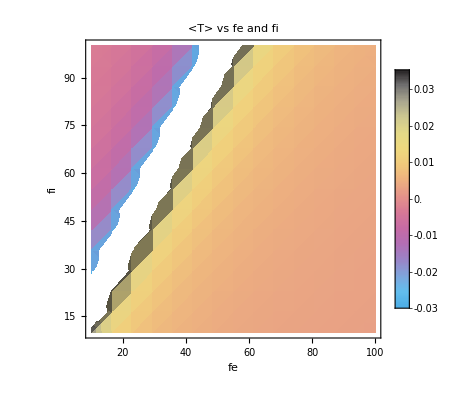

```mathematica
p1 = 0.3;
p2 = 0.2;
k1 = 100;
k2 = 100;
M1 = 500;
M2 = 500;
c1 = 0.01;
c2 = 0.008;
tauv = 1;
vth = 0.2;
numinit1= 10;
numinit2 = 10;

DensityPlot[1/Tmean[f1, f2], {f1, numinit1, 100}, {f2, numinit2, 100}, ColorFunction-> "CMYKColors", PlotLegends -> Automatic, PlotLabel -> "<T> vs fe and fi", FrameLabel -> {"fe", "fi"}]
```

```mathematica
Remove["Global`*"]
Reduce[((k1+f1 p1) (k2+f2 p2) vth)/((-c2 f2 k2 M2 (k1+f1 p1) p2+c1 f1 k1 M1 p1 (k2+f2 p2)) tauv) < 1, {f2}, Assumptions->{}]
```

```mathematica
Reduce[-2+a x^2>0,x,Assumptions->{a>0}]
```

Reduce::optx: Unknown option Assumptions in Reduce[-2+a x^2>0,x,Assumptions→{a>0}].

Reduce[-2+a x^2>0,x,Assumptions→{a>0}]

```mathematica
Assuming[{a>0, b > 0},Reduce[-b+a x^2>0,x]]
```

x∈ℝ&&((b<0&&((a<0&&-√(b/a)<x<√(b/a))||a≥0))||(b≥0&&a>0&&(x<-√(b/a)||x>√(b/a))))

```mathematica
(* --------------------------------------------- Parameters as functions of f -------------------------------------*)
Remove["Global`*"]
k[f_] =  1/(f+1);
bMean[f_] = c pr k[f] M /(f pr + k[f]);
bSquaredMean[f_] = c^2*(pr*(1-pr)*k[f] M / (f pr + k[f]) + (pr*k[f]*M/(f pr + k[f])^2));

eq1= {vMean'[t] == -vMean[t]/tauv + f*bMean[f], vMean[0] == 0};
sol= FullSimplify[DSolve[eq1, vMean[t], t]] ;
vMean[t_] = vMean[t] /. First[sol];
eq2 ={vSquaredMean'[t] == (-2/tauv)*vSquaredMean[t] + 2*f*bMean[f]*vMean[t]+ f*bSquaredMean[f], vSquaredMean[0] == 0};
sol = FullSimplify[DSolve[eq2, vSquaredMean[t], t]];
Print["vSquaredMean"];
vSquaredMean[t_] = vSquaredMean[t] /. First[sol];

vMean0 = 0;
vSquaredMeanTMean[f_] = vSquaredMean[Tmean[f]];
vTmean = vth;
CVvSquaredTmean[f_] =  (vSquaredMeanTMean[f] - vTmean^2)/vTmean^2;
(*dvdtMean= -vth/tauv;*)
dvdtMean[f_] = -1/tauv*vth + f bMean[f];
Print["<T>"]
Tmean [f_]= tauv*Log[(1-vMean0/(tauv*f*bMean[f]))/(1-vth/(tauv*f*bMean[f]))]
Print["CVT2"]
CVTsquared[f_] = FullSimplify[vth^2/(Tmean[f]^2)*dvdtMean[f]^(-2)*CVvSquaredTmean[f]]
```

vSquaredMean

<T>

tauv Log[1/(1-((1+f) (1/(1+f)+f pr) vth)/(c f M pr tauv))]

CVT2

((-2+f (-1+pr)+pr) (1+f pr) (1+f (1+f) pr) vth (vth+f pr (-2 c M tauv+vth+f vth)))/(2 f M pr tauv (vth+f pr (-c M tauv+vth+f vth))^2 Log[(c f M pr tauv)/(c f M pr tauv-(1+f (1+f) pr) vth)]^2)

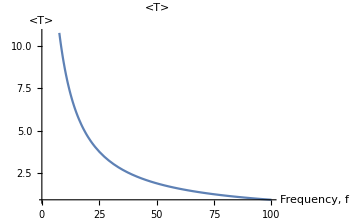
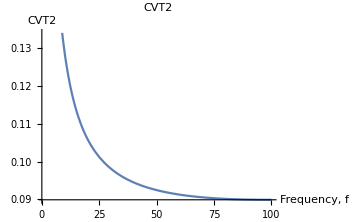

```mathematica
c = 0.02;
pr = 0.2;
M = 1000;

vth = 0.2;
tauv = 10;

fmin = 1;
fmax = 100;
plt1 = Plot[1/Tmean[f],{f,fmin, fmax},PlotLabel->("<T>"), AxesLabel  -> {"Frequency, f", "<T>"}, ImageSize -> Medium];
plt2 = Plot[CVTsquared[f], {f, fmin, fmax},PlotLabel->("CVT2"), AxesLabel-> {"Frequency, f", "CVT2"}, ImageSize -> Medium];
Row[{plt1, plt2}]
```